# 2 species Velocity in terms of Lambdas

## Solving for the velocity

Defining determinant, d/dk of determinant given ds/dk =s/k equations

```mathematica
ClearAll["Global`*"]
 (*definition of determinant as a function of s and k *)
detA[s_,k_]=(s+v1*k+-L11)*(s+v2*k+-L22)-L12*L21;
 (*derivative of determinant with condition that ds/dk=0 & other parameters constant*)
dkDetA[s_,k_]:=Dt[detA[s,k],k, Constants->{v1,v2,L11,L22,L12,L21}]/.Dt[s,k,Constants->{v1,v2,L11,L22,L12,L21}]->s/k
(*to solve detA=0 and dkDetA =0, add equations to eliminate s^2 term*)
eqnForSA[s_,k_]:=Collect[2*detA[s,k] -k*dkDetA[s,k],s]
```

Solving the equations, and then assigning the results

```mathematica
skRootsL=Solve[{detA[s,k]==0,eqnForSA[s,k]==0},{s,k}];
```

```mathematica
s1=s/.skRootsL[[1]];
s2=s/.skRootsL[[2]];
k1=k/.skRootsL[[1]];
k2=k/.skRootsL[[2]];
(*Define velocity and evaluate both velocities, v1 goes to left, v2 to the right*)
velocity[s_,k_]:=-s/k
vel1=FullSimplify[velocity[s1,k1]];
vel2=FullSimplify[velocity[s2,k2]];
```

## Checking solution for velocity, s, and k in the paper.

```mathematica
Q=L12*L21/(L12*L21-L11*L22);
Q2=L11*L22/(L12*L21-L11*L22);
s1Paper=-((L22*v1-L11*v2)*(v1-v2)+(L22*v1+L11*v2)*Abs[v1-v2]*Sqrt[Q] ) / (  Q2*(v1-v2)^2     );
s2Paper=-( (L22*v1-L11*v2)*(v1-v2)-(L22*v1+L11*v2)*Abs[v1-v2]*Sqrt[Q] ) / (  Q2*(v1-v2)^2    );
k1Paper=( (L22-L11)*(v1-v2)+(L22+L11)*Abs[v1-v2]*Sqrt[Q] ) / (  Q2*(v1-v2)^2    );
k2Paper=( (L22-L11)*(v1-v2)-(L22+L11)*Abs[v1-v2]*Sqrt[Q] ) / ( Q2*(v1-v2)^2     );
(*both numerator and denominator have \pm is the correct eqn*)
v1Paper=( (L22*v1-L11*v2)+(L22*v1+L11*v2)*Sign[v1-v2]*Sqrt[Q] ) / (  (L22-L11)+(L22+L11)*Sign[v1-v2]*Sqrt[Q]    );
v2Paper=( (L22*v1-L11*v2)-(L22*v1+L11*v2)*Sign[v1-v2]*Sqrt[Q] ) / (  (L22-L11)-(L22+L11)*Sign[v1-v2]*Sqrt[Q]    );
```

Keisuke - April 5, 2020 new velocity solutions below

```mathematica
Q=L12*L21/(L12*L21-L11*L22);
v1Paper=( (L22*v1-L11*v2)-(L22*v1+L11*v2)*Sign[v1-v2]*Sign[L11+L22]*Sqrt[Q] ) / (  -(L11-L22)-Abs[L22+L11]*Sign[v1-v2]*Sqrt[Q] );
v2Paper=( (L22*v1-L11*v2)+(L22*v1+L11*v2)*Sign[v1-v2]*Sign[L11+L22]*Sqrt[Q] ) / (  -(L11-L22)+Abs[L22+L11]*Sign[v1-v2]*Sqrt[Q] );
Simplify[v1Paper,{L11+L22<0}]
```

(L22 v1-L11 v2+√((L12 L21)/(L12 L21-L11 L22)) (L22 v1+L11 v2) Sign[v1-v2])/(-L11+L22+(L11+L22) √((L12 L21)/(L12 L21-L11 L22)) Sign[v1-v2])

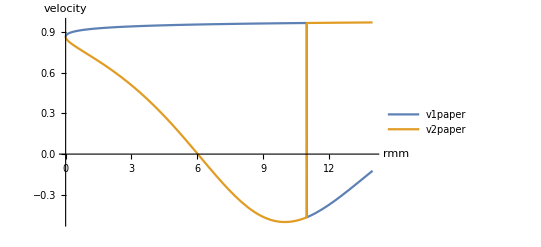

```mathematica
fM= 10;
fP=1;
vM=-.5;
vP=1.;

Plot[{v1Paper/.{v1->vP,v2->vM,L11->-fP ,L22->rmm-fM ,L12-> fM,L21->fP },v2Paper/.{v1->vP,v2->vM,L11->-fP ,L22->rmm-fM ,L12-> fM,L21->fP }},{rmm,0,14},PlotLegends->{"v1paper", "v2paper"}, AxesLabel->{"rmm","velocity"}]
```

analyze the L11+L22<0 and L11+L22>0 cases separately, this identifies a consistent solution for either case

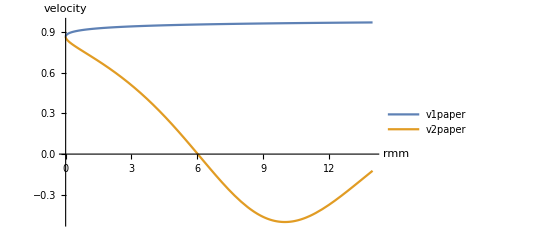

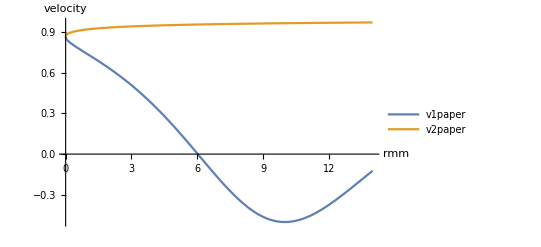

(L22 v1-L11 v2+√((L12 L21)/(L12 L21-L11 L22)) (L22 v1+L11 v2) Sign[v1-v2])/(-L11+L22+(L11+L22) √((L12 L21)/(L12 L21-L11 L22)) Sign[v1-v2])

```mathematica
Plot[{Simplify[v1Paper,{L11+L22<0}]/.{v1->vP,v2->vM,L11->-fP ,L22->rmm-fM ,L12-> fM,L21->fP },Simplify[v2Paper,{L11+L22<0}]/.{v1->vP,v2->vM,L11->-fP ,L22->rmm-fM ,L12-> fM,L21->fP }},{rmm,0,14},PlotLegends->{"v1paper", "v2paper"}, AxesLabel->{"rmm","velocity"}]
Plot[{Simplify[v1Paper,{L11+L22>0}]/.{v1->vP,v2->vM,L11->-fP ,L22->rmm-fM ,L12-> fM,L21->fP },Simplify[v2Paper,{L11+L22>0}]/.{v1->vP,v2->vM,L11->-fP ,L22->rmm-fM ,L12-> fM,L21->fP }},{rmm,0,14},PlotLegends->{"v1paper", "v2paper"}, AxesLabel->{"rmm","velocity"}]
Simplify[v1Paper,{L11+L22<0}]
```

```mathematica
v10=10;
v20=-10;
L110=-0.1;
L120=1.1;
L210=1.;
L220=-0.7;
Simplify[vel1-v1Paper/.{v1->v10,v2->v20,L11->L110,L12->L120,L21->L210,L22->L220}]
Simplify[vel2-v2Paper/.{v1->v10,v2->v20,L11->L110,L12->L120,L21->L210,L22->L220}]
Simplify[k2-k2Paper/.{v1->v10,v2->v20,L11->L110,L12->L120,L21->L210,L22->L220}]
Simplify[s2-s2Paper/.{v1->v10,v2->v20,L11->L110,L12->L120,L21->L210,L22->L220}]
Simplify[k1-k1Paper/.{v1->v10,v2->v20,L11->L110,L12->L120,L21->L210,L22->L220}]
Simplify[s1-s1Paper/.{v1->v10,v2->v20,L11->L110,L12->L120,L21->L210,L22->L220}]

L110=-0.;
vel1/.{v1->v10,v2->v20,L11->L110,L12->L120,L21->L210,L22->L220}
vel2/.{v1->v10,v2->v20,L11->L110,L12->L120,L21->L210,L22->L220}
```

-5.32907×10^-15

8.88178×10^-16

# Deriving velocity equations in for only r++, r--, r+-, r-+ and asymptotic expressions when these rates are either small or large

## (with sign convention in vp and vm.Equations are not in terms of lambdas.)

```mathematica
ClearAll["Global`*"]
(*definition of determinant as a function of s and k *)
detAr[s_,k_]=(s+vp*k+fp-rpp)*(s-vm*k+fm-rmm)-(fm+rpm)*(fp+rmp);
 (*derivative of determinant with condition that ds/dk=0 & other parameters constant*)
dkDetAr[s_,k_]:=Dt[detAr[s,k],k, Constants->{vp,fp,rpp,vm,fm,rmm,rpm,rmp}]/.Dt[s,k,Constants->{fm,fp,rmm,rmp,rpm,rpp,vm,vp}]->s/k
(*to solve detAr=0 and dkDetAr =0, add equations to eliminate s^2 term*)
eqnForS[s_,k_]:=Collect[2*detAr[s,k] -k*dkDetAr[s,k],s]
```

```mathematica
skRootsC0=Solve[{detAr[s,k]==0,eqnForS[s,k]==0},{s,k}];
s1C0=s/.skRootsC0[[1]];
s2C0=s/.skRootsC0[[2]];
k1C0=k/.skRootsC0[[1]];
k2C0=k/.skRootsC0[[2]];
(*Define velocity and evaluate both velocities*)
velocity[s_,k_]:=-s/k
v1C0=velocity[s1C0,k1C0];
v2C0=velocity[s2C0,k2C0];
```

### 1. v++

```mathematica
vel1pp[x_]:=Simplify[v1C0/.{rmm->0, rpm->0, rmp->0, rpp->x }];
vel2pp[x_]:=Simplify[v2C0/.{rmm->0, rpm->0, rmp->0 ,rpp->x }];
```

Series expansion at x=0:

```mathematica
a1=Simplify[Series[vel1pp[x],{x,0,1}],{(vm+vp)>0, x>0, fm>0, fp>0}]
a2=Simplify[Series[vel2pp[x],{x,0,1}],{(vm+vp)>0, x>0,fm>0,fp>0}]
a1-a2
```

(-fp vm+fm vp)/(fm+fp)-(2 (fm √fp (vm+vp)) √x)/(fm+fp)^2-(fm (fm-3 fp) (vm+vp) x)/(fm+fp)^3+(4 fm (fm-fp) √fp (vm+vp) x^(3/2))/(fm+fp)^4+O[x]^2

(-fp vm+fm vp)/(fm+fp)+(2 fm √fp (vm+vp) √x)/(fm+fp)^2-(fm (fm-3 fp) (vm+vp) x)/(fm+fp)^3-(4 (fm (fm-fp) √fp (vm+vp)) x^(3/2))/(fm+fp)^4+O[x]^2

-(4 (fm √fp (vm+vp)) √x)/(fm+fp)^2+(8 fm (fm-fp) √fp (vm+vp) x^(3/2))/(fm+fp)^4+O[x]^2

The limit of v++ as r++ goes to f+ is vp as expected. BUT v1 and v2 both asymptote to vp . this is because the linear solution assumptions break at this point.
For vm+vp >0, vel2pp,  the right moving wave is what matters.
In the expansion around f+, we notice that the linear term in vel1pp has a denominator that is zero. this is fine because this term described the left-moving wave actually and so the blow up is due to the jump of the left moving wave to the velocity v+
The equation we care abut is vel2pp, the linear term goes to zero (denominator diverges), and so we have a quadratic dependence at r++=f+

```mathematica
Limit[vel1pp[x],x->fp]
Limit[vel2pp[x],x->fp]
FullSimplify[Series[vel1pp[x],{x,fp,2}]]
FullSimplify[Series[vel2pp[x],{x,fp,2}]]
```

vp

vp

vp+(x-fp)/(fm/(vm+vp)-(2 fm^3 fp)/(fm^2 fp (vm+vp)+√(fm^4 fp^2 (vm+vp)^2)))+(fm (vm+vp)^2 (x-fp)^2)/(-2 fm^2 fp (vm+vp)+2 √(fm^4 fp^2 (vm+vp)^2))+O[x-fp]^3

vp+(x-fp)/(fm/(vm+vp)-(2 fm^3 fp)/(fm^2 fp (vm+vp)-√(fm^4 fp^2 (vm+vp)^2)))-((fm (vm+vp)^2) (x-fp)^2)/(2 (fm^2 fp (vm+vp)+√(fm^4 fp^2 (vm+vp)^2)))+O[x-fp]^3

The quadratic term in vel2++ is  ( for vm+vp>0)

```mathematica
Simplify[-(fm*(vm + vp)^2)/(2*(fm^2*fp*(vm + vp) + Sqrt[fm^4*fp^2*(vm + vp)^2])),{(vm+vp)>0, fm>0, fp>0}]
```

-(vm+vp)/(4 fm fp)

Plotting the two branches of the solution. The larger one is the right moving front. Note that this  solution is physically valid for rpp<fp
For rpp>fp, the front velocity saturates at vp

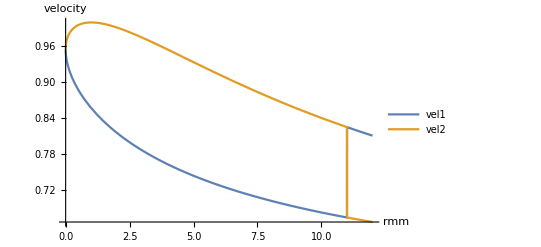

```mathematica
rPM=0.0;
rMM=0.0;
rMP=0.0;
fM= 10;
fP=1;
vM=-.5;
vP=1.;

Plot[{v1C0/.{fm->fM,vp->vP,vm->vM,rmp->rMP,fp->fP , rpm->rPM,rmm->rMM},v2C0/.{fm->fM,vp->vP,vm->vM,rmp->rMP ,fp->fP , rpm->rPM,rmm->rMM}},{rpp,0,12},PlotLegends->{"vel1", "vel2"}, AxesLabel->{"rmm","velocity"}]
```

### 2. v+-

```mathematica
vel1pm[x_]:=Simplify[v1C0/.{rmm->0, rpp->0, rmp->0, rpm->x },{fm>0, fp>0}];
vel2pm[x_]:=Simplify[v2C0/.{rmm->0, rpp->0, rmp->0 ,rpm->x },{fm>0, fp>0}];
```

For vm+ vp>0, vel2pm is the right moving wave. For vm+vp <0, vel1 is the right moving wave.

```mathematica
Limit[vel1pm[x],x->Infinity];
Limit[vel2pm[x],x->Infinity];
Simplify[Limit[vel1pm[x],x->Infinity],{(vm+vp)>0}]
Simplify[Limit[vel2pm[x],x->Infinity],{(vm+vp)>0}]
Simplify[Limit[vel1pm[x],x->Infinity],{(vm+vp)<0}]
Simplify[Limit[vel2pm[x],x->Infinity],{(vm+vp)<0}]
```

-vm

vp

vp

-vm

Series expansion at small x:

```mathematica
a1=Simplify[Series[vel1pm[x],{x,0,1}],{(vm+vp)>0, x>0}]
a2=Simplify[Series[vel2pm[x],{x,0,1}],{(vm+vp)>0, x>0}]
a1-a2
```

(-fp vm+fm vp)/(fm+fp)-(2 (√fm fp (vm+vp)) √x)/(fm+fp)^2-(2 ((fm-fp) fp (vm+vp)) x)/(fm+fp)^3-(fp (fm^2-6 fm fp+fp^2) (vm+vp) x^(3/2))/(√fm (fm+fp)^4)+O[x]^2

(-fp vm+fm vp)/(fm+fp)+(2 √fm fp (vm+vp) √x)/(fm+fp)^2-(2 ((fm-fp) fp (vm+vp)) x)/(fm+fp)^3+(fp (fm^2-6 fm fp+fp^2) (vm+vp) x^(3/2))/(√fm (fm+fp)^4)+O[x]^2

-(4 (√fm fp (vm+vp)) √x)/(fm+fp)^2-(2 (fp (fm^2-6 fm fp+fp^2) (vm+vp)) x^(3/2))/(√fm (fm+fp)^4)+O[x]^2

Series function breaks when expanding at infinity,

```mathematica
Simplify[Series[vel1pm[x],{x,Infinity,1}],{(vm+vp)<0, x>0}]
(*Simplify[Series[vel2pm[x],{x,Infinity,1}],{vp>0, vm<0,(vm+vp)>0,fm>0, fp>0,x>0}]*)
```

(2 (fm^2+fp^2) (-fp^2 vm+fm^2 vp-fm fp (vm+3 vp)))/(fm-fp)^4+(fm (fm+fp)^2 (fp vm+fm vp))/((fm-fp)^3 x)+O[1/x]^2

So the y=1/x is substituted before using series to expand around 0 fro positive y. this works better,.

```mathematica
vel2pmInv[y_]:= vel2pm[1/y]
Limit[Simplify[vel2pmInv[y],{(vm+vp)>0, y>0, fm>0, fp>0}], y->0]
Series[Simplify[vel2pmInv[y],{(vm+vp)>0, y>0, fm>0, fp>0}],{y,0,1}]
vInvApprox=Normal[Series[Simplify[vel2pmInv[y],{(vm+vp)>0, y>0, fm>0}],{y,0,1}]]
vApprox=vInvApprox/.{y->1./rpm }
```

vp

vp+(-(fp vm)/4-(fp vp)/4) y+O[y]^2

vp+(-(fp vm)/4-(fp vp)/4) y

vp+(1. (-(fp vm)/4-(fp vp)/4))/rpm

#### Verifying solution by plotting against the full solution.

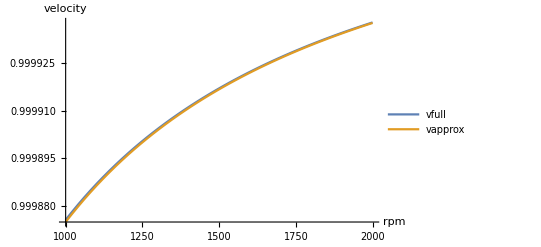

```mathematica
rMM=.0;
rPP=0.0;
rMP=0.;
fM=10.;
fP=1.;
vM=-.5;
vP=1.;

Plot[{v2C0/.{fm->fM,vp->vP,vm->vM,rmp->rMP,fp->fP , rmm->rMM,rpp->rPP},vApprox/.{fm->fM,vp->vP,vm->vM,rmp->rMP ,fp->fP , rmm->rMM,rpp->rPP}},{rpm,1000,2000},PlotLegends->{"vfull", "vapprox"}, AxesLabel->{"rpm","velocity"}]
```

### 3. v-+

```mathematica
vel1mp[x_]:=Simplify[v1C0/.{rmm->0, rpp->0, rpm->0, rmp->x },{fm>0, fp>0}];
vel2mp[x_]:=Simplify[v2C0/.{rmm->0, rpp->0, rpm->0 ,rmp->x },{fm>0, fp>0}];
```

Series expansion at small x:

```mathematica
a1=Simplify[Series[vel1mp[x],{x,0,1}],{(vm+vp)>0, x>0}]
a2=Simplify[Series[vel2mp[x],{x,0,1}],{(vm+vp)>0, x>0}]
a1-a2
```

(-fp vm+fm vp)/(fm+fp)-(2 (fm √fp (vm+vp)) √x)/(fm+fp)^2-(2 (fm (fm-fp) (vm+vp)) x)/(fm+fp)^3-(fm (fm^2-6 fm fp+fp^2) (vm+vp) x^(3/2))/(√fp (fm+fp)^4)+O[x]^2

(-fp vm+fm vp)/(fm+fp)+(2 fm √fp (vm+vp) √x)/(fm+fp)^2-(2 (fm (fm-fp) (vm+vp)) x)/(fm+fp)^3+(fm (fm^2-6 fm fp+fp^2) (vm+vp) x^(3/2))/(√fp (fm+fp)^4)+O[x]^2

-(4 (fm √fp (vm+vp)) √x)/(fm+fp)^2-(2 (fm (fm^2-6 fm fp+fp^2) (vm+vp)) x^(3/2))/(√fp (fm+fp)^4)+O[x]^2

```mathematica
Simplify[Limit[vel1mp[x],x->Infinity],{(vm+vp)>0}]
Simplify[Limit[vel2mp[x],x->Infinity],{(vm+vp)>0}]
Simplify[Limit[vel1mp[x],x->Infinity],{(vm+vp)<0}]
Simplify[Limit[vel2mp[x],x->Infinity],{(vm+vp)<0}]
```

-vm

vp

vp

-vm

```mathematica
vel2mpInv[y_]:= vel2mp[1/y]
Limit[Simplify[vel2mpInv[y],{(vm+vp)>0, y>0, fm>0, fp>0}], y->0]
Series[Simplify[vel2mpInv[y],{(vm+vp)>0, y>0, fm>0, fp>0}],{y,0,1}]
vInvApprox=Normal[Series[Simplify[vel2mpInv[y],{(vm+vp)>0, y>0}],{y,0,1}]]
vApprox=vInvApprox/.{y->1./rmp }
```

vp

vp+((-fp^2 vm-fp^2 vp) y)/(4 fm)+O[y]^2

vp+((-fp^2 vm-fp^2 vp) y)/(4 fm)

vp+(0.25 (-fp^2 vm-fp^2 vp))/(fm rmp)

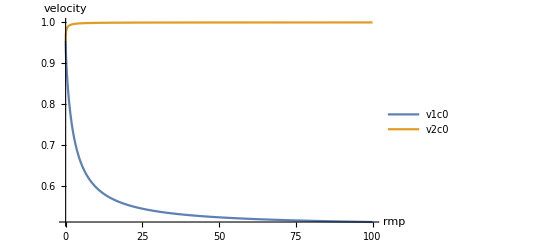

```mathematica
rMM=.0;
rPP=0.0;
rPM=0.;
fM=10.;
fP=1.;
vM=-.5;
vP=1.;

Plot[{v1C0/.{fm->fM,vp->vP,vm->vM,rpm->rPM,fp->fP , rmm->rMM,rpp->rPP},v2C0/.{fm->fM,vp->vP,vm->vM,rpm->rPM ,fp->fP , rmm->rMM,rpp->rPP}},{rmp,0,100},PlotLegends->{"v1c0", "v2c0"}, AxesLabel->{"rmp","velocity"}]
```

### 4. v--

```mathematica
vel1mm[x_]:=Simplify[v1C0/.{rpp->0, rpm->0, rmp->0, rmm->x }]
vel2mm[x_]:=Simplify[v2C0/.{rpp->0, rpm->0, rmp->0 ,rmm->x }]

FullSimplify[v1C0/.{rpp->0, rpm->0, rmp->0, rmm->x },{fp>0,vp+vm>0,fm+fp-x>0}]
FullSimplify[v2C0/.{rpp->0, rpm->0, rmp->0, rmm->x },{fp>0,vp+vm>0,fm+fp-x>0}]
```

(vp (fm-x) (-x+√(fm x))-fp vm (x+√(fm x)))/(x (x-√(fm x))+fm (-x+√(fm x))+fp (x+√(fm x)))

(fp vm (x-√(fm x))+vp (fm-x) (x+√(fm x)))/(fp (-x+√(fm x))+fm (x+√(fm x))-x (x+√(fm x)))

Series expansion at small x:

```mathematica
a1=Simplify[Series[vel1mm[x],{x,0,1}],{(vm+vp)>0, x>0,fm>0,fp>0}]
a2=Simplify[Series[vel2mm[x],{x,0,1}],{(vm+vp)>0, x>0,fm>0,fp>0}]
a1-a2
```

(-fp vm+fm vp)/(fm+fp)-(2 (√fm fp (vm+vp)) √x)/(fm+fp)^2-((3 fm-fp) fp (vm+vp) x)/(fm+fp)^3-(4 (√fm (fm-fp) fp (vm+vp)) x^(3/2))/(fm+fp)^4+O[x]^2

(-fp vm+fm vp)/(fm+fp)+(2 √fm fp (vm+vp) √x)/(fm+fp)^2-((3 fm-fp) fp (vm+vp) x)/(fm+fp)^3+(4 √fm (fm-fp) fp (vm+vp) x^(3/2))/(fm+fp)^4+O[x]^2

-(4 (√fm fp (vm+vp)) √x)/(fm+fp)^2-(8 (√fm (fm-fp) fp (vm+vp)) x^(3/2))/(fm+fp)^4+O[x]^2

Both velocities limit to vp  because it the left-moving linear velocity branch breaks at rmm=fm . Only one branch makes sense

```mathematica
Limit[Simplify[vel1mm[x],{(vm+vp)>0}],x->fm]
Limit[Simplify[vel2mm[x],{(vm+vp)>0}],x->fm]
Limit[Simplify[vel1mm[x],{(vm+vp)<0}],x->fm]
Limit[Simplify[vel2mm[x],{(vm+vp)<0}],x->fm]

Limit[Simplify[vel1mm[x],{(vm+vp)>0}],x->Infinity]
Limit[Simplify[vel2mm[x],{(vm+vp)>0}],x->Infinity]
Limit[Simplify[vel1mm[x],{(vm+vp)<0}],x->Infinity]
Limit[Simplify[vel2mm[x],{(vm+vp)<0}],x->Infinity]
```

-vm

-vm

-vm

«1 more identical outputs»

vp

vp

vp

«1 more identical outputs»

to figure out which of the velocity branches broke, we plot the solutions

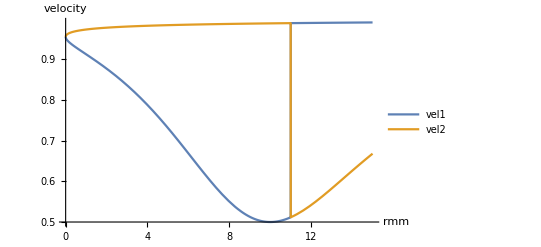

```mathematica
rPM=0.0;
rPP=0.0;
rMP=0.0;
fM= 10;
fP=1;
vM=-.5;
vP=1.;
Plot[{v1C0/.{fm->fM,vp->vP,vm->vM,rmp->rMP,fp->fP , rpm->rPM,rpp->rPP},v2C0/.{fm->fM,vp->vP,vm->vM,rmp->rMP ,fp->fP , rpm->rPM,rpp->rPP}},{rmm,0,15},PlotLegends->{"vel1", "vel2"}, AxesLabel->{"rmm","velocity"}]
```

```mathematica
Simplify[Series[vel1mm[x],{x,Infinity,1}]]
Simplify[Series[vel2mm[x],{x,Infinity,1}]]
vmmApprox=Simplify[Normal[Series[vel1mm[x],{x,Infinity,1}]]/.{x->rmm}]
```

vp-(fp (vm+vp))/x+O[1/x]^2

vp-(fp (vm+vp))/x+O[1/x]^2

vp-(fp (vm+vp))/rmm

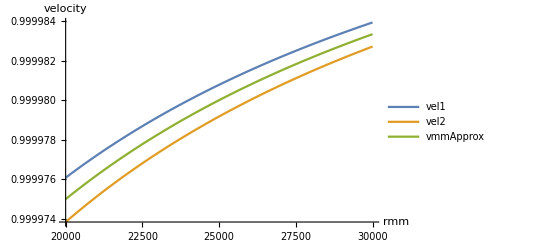

```mathematica
Plot[{v1C0/.{fm->fM,vp->vP,vm->vM,rmp->rMP,fp->fP , rpm->rPM,rpp->rPP},v2C0/.{fm->fM,vp->vP,vm->vM,rmp->rMP ,fp->fP , rpm->rPM,rpp->rPP},
vmmApprox/.{fm->fM,vp->vP,vm->vM,rmp->rMP ,fp->fP , rpm->rPM,rpp->rPP}},{rmm,20000,30000},PlotLegends->{"vel1", "vel2", "vmmApprox"}, AxesLabel->{"rmm","velocity"}]
```

## Pairwise analysis of different modes of replication

non-dimensionalize system with parameters mu, nu, and rho

```mathematica
Vrpponly=(2 √(fp rpp) vm-(fp+rpp) vm+fm vp)/(fm+fp+rpp-2 √(fp rpp));
Vrpmonly=1/((fm+fp)^2+4 fp rpm)(2 fp √(rpm (fm+rpm)) vm-fp (fm+fp+2 rpm) vm+fm (fm+fp) vp+2 fp rpm vp+2 fp √(rpm (fm+rpm)) vp);
Vrmmonly=(-fp vm+(fm+rmm+2 √(fm rmm)) vp)/(fm+fp+rmm+2 √(fm rmm));
Vrmponly=1/((fm+fp)^2+4 fm rmp)(2 fm √(rmp (fp+rmp)) vm-(fp (fm+fp)+2 fm rmp) vm+2 fm √(rmp (fp+rmp)) vp+fm (fm+fp+2 rmp) vp);
parmz={vp->mu,vm->1,fp->1,fm->nu,rpp->rho,rmm->rho,rmp->rho,rpm->rho};
VrpponlyND = Vrpponly/.parmz
VrpmonlyND = Vrpmonly/.parmz
VrmmonlyND = Vrmmonly/.parmz
VrmponlyND = Vrmponly/.parmz
```

(-1+mu nu+2 √rho-rho)/(1+nu-2 √rho+rho)

(-1-nu+mu nu (1+nu)-2 rho+2 mu rho+2 √(rho (nu+rho))+2 mu √(rho (nu+rho)))/((1+nu)^2+4 rho)

(-1+mu (nu+rho+2 √(nu rho)))/(1+nu+rho+2 √(nu rho))

(-1-nu-2 nu rho+2 nu √(rho (1+rho))+2 mu nu √(rho (1+rho))+mu nu (1+nu+2 rho))/((1+nu)^2+4 nu rho)

### 1. V++ vs. V+-

```mathematica
Animate[Plot[{(-1+mu nu+2 √rho-rho)/(1+nu-2 √rho+rho),(-1-nu+mu nu (1+nu)-2 rho+2 mu rho+2 √(rho (nu+rho))+2 mu √(rho (nu+rho)))/((1+nu)^2+4 rho)},{rho,0,1}],{mu,0,2},{nu,0,2},AnimationRunning->False]
Simplify[Solve[(Vrpponly==Vrpmonly)/.parmz,rho],{nu>0&&rho<1&&rho>0&&nu<1}]
```

{{rho→0},{rho→(4 (-2+√nu+nu)^2)/(-4+nu)^2},{rho→(4 (1+√nu)^2)/(2+√nu)^2}}

### 2. V++ vs. V---

```mathematica
Animate[Plot[{(-1+mu nu+2 √rho-rho)/(1+nu-2 √rho+rho),(-1+mu (nu+rho+2 √(nu rho)))/(1+nu+rho+2 √(nu rho))},{rho,0,1},PlotLegends->{"V++", "V--"}, AxesLabel->{"rho","Velocity"}],{mu,0,2},{nu,0,2},AnimationRunning->False]
Simplify[Solve[(Vrpponly==Vrmmonly)/.parmz,nu],{rho>0&&rho<1}]
```

{{nu→(-1+√rho)^2},{nu→((-1+√rho)^2 rho)/(-2+√rho)^2}}

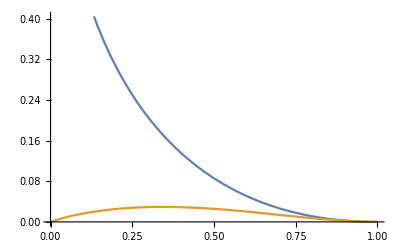

{{mu→1}}

{{mu→1}}

```mathematica
Plot[{(-1+√rho)^2,((-1+√rho)^2 rho)/(-2+√rho)^2},{rho,0,1}]
Simplify[Solve[(-1+mu nu+2 √rho-rho)/(1+nu-2 √rho+rho)==0/.{nu->(-1+√rho)^2},mu],{nu>0&&nu<1,rho>0&&rho<1}]
Simplify[Solve[(-1+mu (nu+rho+2 √(nu rho)))/(1+nu+rho+2 √(nu rho))==0/.{nu->(-1+√rho)^2},mu],{nu>0&&nu<1&&rho>0&&rho<1}]
```

### 3. V++ vs. V-+

```mathematica
Animate[Plot[{(-1+mu nu+2 √rho-rho)/(1+nu-2 √rho+rho),(-1-nu-2 nu rho+2 nu √(rho (1+rho))+2 mu nu √(rho (1+rho))+mu nu (1+nu+2 rho))/((1+nu)^2+4 nu rho)},{rho,0,1},PlotLegends->{"V++", "V-+"}, AxesLabel->{"rho","Velocity"}],{mu,0,2},{nu,0,10},AnimationRunning->False]
Simplify[Solve[(Vrpponly==Vrmponly)/.parmz,nu],{rho>0&&rho<1&&nu>0}]
```

{{nu→0},{nu→-(2 √rho+4 rho^(3/2)-2 rho^2-2 √(rho (1+rho))+rho (-3+4 √(1+rho)-2 √(rho (1+rho))))/(2 √rho+rho-2 √(rho (1+rho)))}}

### 4. V+- vs. V--

```mathematica
Animate[Plot[{(-1-nu+mu nu (1+nu)-2 rho+2 mu rho+2 √(rho (nu+rho))+2 mu √(rho (nu+rho)))/((1+nu)^2+4 rho),(-1+mu (nu+rho+2 √(nu rho)))/(1+nu+rho+2 √(nu rho))},{rho,0,1},PlotLegends->{"V+-", "V--"}, AxesLabel->{"rho","Velocity"}],{mu,0,2},{nu,0,2},AnimationRunning->False]
Simplify[Solve[(Vrpmonly==Vrmmonly)/.parmz,nu],{rho>0}]
```

{{nu→(9 rho)/16}}

### 5. V+- vs. V-+

```mathematica
Animate[Plot[{(-1-nu+mu nu (1+nu)-2 rho+2 mu rho+2 √(rho (nu+rho))+2 mu √(rho (nu+rho)))/((1+nu)^2+4 rho),(-1-nu-2 nu rho+2 nu √(rho (1+rho))+2 mu nu √(rho (1+rho))+mu nu (1+nu+2 rho))/((1+nu)^2+4 nu rho)},{rho,0,1},PlotLegends->{"V+-", "V-+"}, AxesLabel->{"rho","Velocity"}],{mu,0,2},{nu,0,2},AnimationRunning->False]
```

### 6. V-- vs. V-+

```mathematica
Animate[Plot[{(-1+mu (nu+rho+2 √(nu rho)))/(1+nu+rho+2 √(nu rho)),(-1-nu-2 nu rho+2 nu √(rho (1+rho))+2 mu nu √(rho (1+rho))+mu nu (1+nu+2 rho))/((1+nu)^2+4 nu rho)},{rho,0,1},PlotLegends->{"V-+", "V-+"}, AxesLabel->{"rho","Velocity"}],{mu,0,2},{nu,0,1.2},AnimationRunning->False]
```